```mathematica
Experiments with the Chua's Circuit

(*
==Chua's circuit==
the double-scroll attractor (sometimes known as Chua's attractor) is a strange attractor observed from a physical electronic chaotic circuit (generally,Chua's circuit) with a single nonlinear resistor (see Chua's Diode).The double-scroll system is often described by a system of three nonlinear ordinary differential equations and a 3-segment piecewise-linear equation (see Chua's equations).This makes the system easily simulated numerically and easily manifested physically due to Chua's circuits' simple design.
-http://www.chuacircuits.com/
-https://en.wikipedia.org/wiki/Multiscroll_attractor
dx/dt=c1*(y-x-f(x)) // m0: slope in outer region
   dy/dt=c2*(x-y+z)    // m1: slope in inner region
   dz/dt=-c3*y         // b: Breakpoints
   f(x)=m1*x+(m0-m1)/2*(|x+1|-|x-1|)
*)
```

```mathematica
hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_]:=(1/2)*(Tanh[softness (limitValue-x)]+1); (* A soft limiter using a tanh *)

(*Define the chua circuit's differential equations *)
g[x_] := m0 * x + (m1-m0)/2 * (Abs[x+b]-Abs[x-b]);
f[{x_,y_,z_}]:={c1 * (y-x-g[x]),c2*(x-y+z),-c3*y limiter[x]};

(*RK4 Runge Kutta method based on: 
https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods*)
h = 0.001;
RK4 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/2];
k3=h*f[x+k2/2];
k4=h*f[x+k3];
y=x+1/6*(k1+2*k2+2*k3+k4);
x = y;
Return[x]];

x ={-1.5,0,0};
c1=15.6;
c2 =1;
c3 = 28;
m0=-0.714; (*slope in outer region default:-0.714 *)
m1 = -1.143; (*slope in inner region /default: -1.143 *)
b =1; (*Breakpoints *)

limiter = softLim; (* Choose the softlimiter *)
limitValue =2.23;(* 1.9/Period 1 limit cycle // 2.23/Period 4 limit cycle // >2.4/Not limited *)
softness = 7; (* Softness *)

n = 45000;
chuaPlot=Table[RK4,{i,1,n}];

(* Plot limits*)
limPlot = chuaPlot;

lims = limiter[{chuaPlot[[All,1]]}];
limPlot[[All,3]]= Flatten[Transpose[lims]];

Graphics3D[Point[chuaPlot[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot[[All,3]]],Axes->True,BoxRatios->{1,1,1/GoldenRatio}]
```

-Graphics3D-

7 Limiter plot

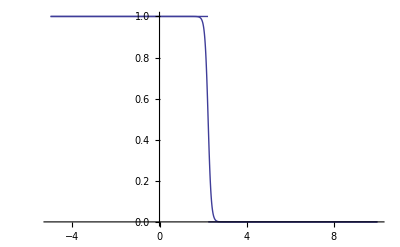

```mathematica
Limiter softness plot
Show[Plot[hardLim[x],{x,-5,10}],Plot[softLim[x],{x,-5,10}]]
```

```mathematica
(*ModelLeg, 0g*)
SetDirectory[NotebookDirectory[]];
chuaData0g = Import["ChuaCircuit-modelLeg-0g-100s.tsv","Data"];
chuaTitle0g = chuaData0g[[1,All]];
chuaPlot0g = Drop[chuaData0g,1];

Show[ListPointPlot3D[{chuaPlot0g},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot0g}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle0g]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g*)
SetDirectory[NotebookDirectory[]];
chuaData1g = Import["ChuaCircuit-modelLeg-1g-100s.tsv","Data"];
chuaTitle1g = chuaData1g[[1,All]];
chuaPlot1g = Drop[chuaData1g,1];

Show[ListPointPlot3D[{chuaPlot1g},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g,without friction, force 1*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction00.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

```mathematica
(*ModelLeg, 1g,friction 1,1,force 5*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force5.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g,friction 1,1,force 2*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force2.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g,friction 1,1,force 1, xzy*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force1-xzy.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
Manipulatable Chua Circuit(Not working yet)
hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_]:=(1/2)*(Tanh[softness (limitValue-x)]+1); (* A soft limiter using a tanh *)

(*Define the chua circuit's differential equations *)
g[x_] := m0 * x + (m1-m0)/2 * (Abs[x+b]-Abs[x-b]);
chuaCircuit[{x_,y_,z_}]:={c1 * (y-x-g[x]),c2*(x-y+z),-c3*y limiter[x]};

(*RK4 Runge Kutta method based on: 
https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods*)
h = 0.001;
RK4 := Module[{y}, 
k1 = h*chuaCircuit[x];
k2 = h*chuaCircuit[x+k1/2];
k3=h*chuaCircuit[x+k2/2];
k4=h*chuaCircuit[x+k3];
y=x+1/6*(k1+2*k2+2*k3+k4);
x = y;
Return[x]];

x ={-1.5,0,0};
limiter = softLim; 

Manipulate[Graphics3D[Point[Table[RK4,{i,1,ControlActive[1000,12000]}],(*Chua Circuit*)
VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@Flatten[Transpose[limiter[Table[RK4,{i,1,ControlActive[1000,12000]}]]]]],(*Limit coloring, the higher the limit, the stronger the color*)
Axes->True,BoxRatios->{1,1,1/GoldenRatio}],
{{c1,13.7},0,20,0.01,Appearance->"Labeled"},
{{c2,1},0,30,0.01,Appearance->"Labeled"},
{{c3,29},0,30,0.01,Appearance->"Labeled"},
{{m0,-0.714},-1,1,0.01,Appearance->"Labeled"},(*slope in outer region of the chua piecewise-linear resistor default:-0.714 *)
{{m1,-1.143},-2,2,0.01,Appearance->"Labeled"},(*slope in inner region of the chua piecewise-linear resistor /default: -1.143 *)
{{b,1},0,4,0.1,Appearance->"Labeled"}, (*Breakpoints *)
{{limitValue,10},-3,10,0.001,Appearance->"Labeled"},(* 1.9/Period 1 limit cycle // 2.23/Period 4 limit cycle // >2.4/Not limited *)
{{softness,7},0,10,0.1,Appearance->"Labeled"}]
```

Chua Circuit Manipulatable Not working yet

```mathematica
Set current working directory to Notebook directory
SetDirectory[NotebookDirectory[]];
```

```mathematica
NotebookDirectory[]
```

/home/leviathan/git/minemonics/Minemonics/doc/measurements/